Define expected reward function R(t,s,cx_d) in terms of decision rule boundary t, shape parameter s, and impact of distractor cx_d.

```mathematica
x={6,12,18,24,32,38,44,50};
```

```mathematica
R[t_,s_,cxd_]:=Total[(LogisticSigmoid[(t-#)/s] + LogisticSigmoid[-(t+#-56)/s]+LogisticSigmoid[(t-#-cxd)/s] + LogisticSigmoid[-(t+#-56-cxd)/s])&/@x[[1;;4]]];
```

```mathematica
Plot3D[ R[t,s,cxd]/.s->0.5, {t,6,50},{cxd,-50,10}, MeshFunctions->{#3&}, PlotPoints->{50, 50}]
```

-Graphics3D-

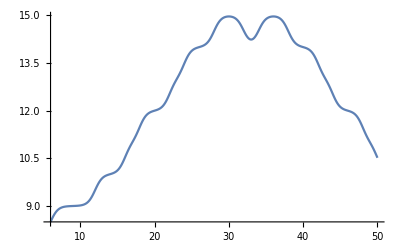

```mathematica
Plot[ R[t,s,cxd]/.{s->0.5, cxd->10}, {t,6,50}, PlotPoints->1000]
```

```mathematica
R[33, 0.5, 10]
```

14.2383

```mathematica
R[32, 0.5, 10]
```

14.5176

```mathematica
R[34, 0.5, 10]
```

14.5176